## Fundamental Diagram

```mathematica
GetSpeedAndDensityOfSingleRoad = (edgeId) ↦ Module[{queryNodeCapacity, fluxValues, densityValues},
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
fluxValues = Normal@Transpose[queryNodeCapacity]["flux"];
densityValues = Normal@Transpose[queryNodeCapacity]["density"];

{densityValues, fluxValues} // Transpose
];

PlotCongestionOfSingleRoad = (edgeId) ↦ Module[{},
ListPlot[GetSpeedAndDensityOfSingleRoad[edgeId], PlotRange->All]
];
```

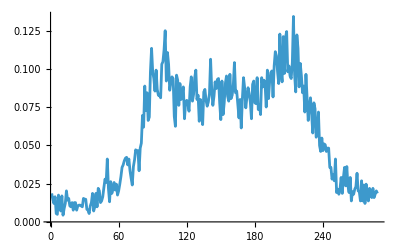

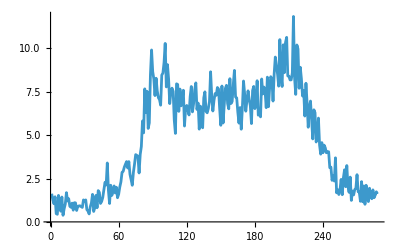

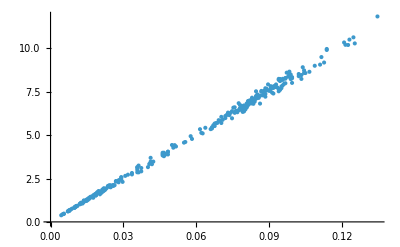

```mathematica
testRoad = GetSpeedAndDensityOfSingleRoad[55255453];
ListLinePlot[testRoad[[;;, 1]]]
ListLinePlot[testRoad[[;;, 2]]]
ListPlot[testRoad]
```

```mathematica
validNodes = VertexList[g];
$DefaultParallelKernels= {8};
CloseKernels[]
LaunchKernels[];
heatmapPoints = ParallelMap[GetSpeedAndDensityOfSingleRoad, validNodes, Method->"ItemsPerEvaluation" -> 10];
```

```mathematica
Export["heatmapPoints.mx", heatmapPoints];
```

```mathematica
heatmapPoints = Import["C:\\Users\\Matteo\\Documents\\heatmapPoints.mx"];
```

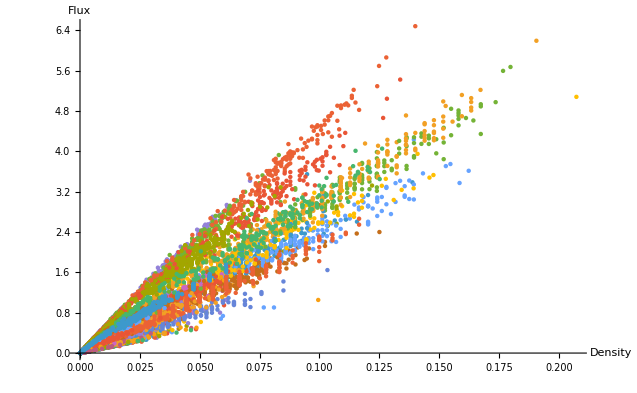

```mathematica
ListPlot[heatmapPoints[[200;;500]], AxesLabel->{"Density", "Flux"}, PlotStyle->PointSize[.005], PlotRange->Full]
```